```mathematica
ClearAll["Global`*"]
r=290;
h=38.15;
thp=22.5°;
b1=h/Tan[thp];
r1=Sqrt[h^2+b1^2];
sol=Solve[Cos[x]/Cos[thp]-b1/(r*Cos[thp])==Sin[x]/Sin[thp],x,InverseFunctions->True]
th=(x/.sol)[[2]]
th/Degree
x=r*Cos[th]+40*Cos[thp]
y=r*Sin[th]+40*Sin[thp]
```

{{x→-2.62705},{x→0.27086}}

0.27086

15.5191

316.382

92.8998

```mathematica
ClearAll["Global`*"]
c=38.15;
a=290;
al=67.5°;
b=c*Cos[al]+Sqrt[(c*Cos[al])^2+a^2-c^2]
x=(b+40)*Cos[al]-c
y=(b+40)*Sin[al]
```

302.45

92.8998

316.382

316.382

-90.9863

92.8998

316.382

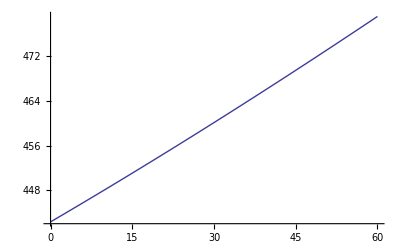

{{xx→-552.247},{xx→47.0382}}

1145.27

```mathematica
ClearAll["Global`*"]
r=290;
h=38.15;
thp=22.5°;
b1=h/Tan[thp];
r1=Sqrt[h^2+b1^2];
sol=Solve[Cos[x]/Cos[thp]-b1/(r*Cos[thp])==Sin[x]/Sin[thp],x,InverseFunctions->True];
th=(x/.sol)[[2]];
th/Degree;
xb[len_]=r*Cos[th]+len*Cos[thp];
yb[len_]=-1(r*Sin[th]+len*Sin[thp]);
zb=0;
xm[len_]=r*Cos[th]+len*Cos[thp];
ym[len_]=r*Sin[th]+len*Sin[thp];
zm=1100;
c=38.15;
a=290;
al=67.5°;
b=c*Cos[al]+Sqrt[(c*Cos[al])^2+a^2-c^2];
xt[len_]=(b+len)*Cos[al]-c;
yt[len_]=(b+len)*Sin[al];
zt=0;
R[aa1_,bb1_,cc1_,aa2_,bb2_,cc2_]=Sqrt[(aa1-aa2)^2+(bb1-bb2)^2+(cc1-cc2)^2];
xb[40]
yb[35]
xt[40]
yt[40]
Plot[R[xb[40],yb[40],zb,xt[xx],yt[xx],zt],{xx,0,60}]
Solve[R[xb[40],yb[40],zb,xt[xx],yt[xx],zt]==470.77,xx]
R[316.3821217529913,92.89976572246482,1100,xt[47.04],yt[47.04],0]
```